```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
SIGMA=Table[0,10,10];
For[i=1,i≤10,i++,SIGMA[[i,i]]=1/4^(i-1)];
U[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=N[1/2 Simplify[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}.LinearSolve[SIGMA,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}]]];
dU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=GradientG[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
ddU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=HessianH[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
```

501 1.39498×10^6 57.716 0.1 0.316228 51059. 1.44604×10^6 1.74818×10^6 0.0000357434 0.00089543 True {1,4,11} {1,11}

1002 242466. 7.59003 0.361738 0.344746 2426.75 244394. 244892. 9.41234×10^-6 0.000984973 False {1,2,4,6,11} {1,11}

1503 84221.4 49.3004 0.383082 0.40748 848.102 85069.5 84873. 7.07163×10^-6 0.000814027 True {1,4,5,8,11} {1,11}

2004 36787.8 9.94115 0.494519 0.440974 374.486 37312.8 37162.3 0.0000113889 0.00158631 False {1,4,5,10,11} {1,11}

2505 18440.4 44.1866 0.672073 0.197068 180.288 18620.7 18422.9 7.7788×10^-6 0.00232252 True {1,3,5,11} {1,11}

3006 10207.3 9.04773 0.563798 0.403355 119.018 10381.3 10326.3 9.41234×10^-6 0.00255477 False {1,7,9,11} {1,11}

3507 6354.6 48.9085 0.425842 0.381567 73.0011 6427.6 6517.36 0.0000221938 0.00340039 True {1,3,4,11} {1,11}

4008 4671.81 9.48678 0.559955 0.384299 53.2584 4660.79 4725.07 0.0000244132 0.00411448 False {1,2,3,4,6,10,11} {1,11}

4509 3280.37 56.6918 0.791293 0.297522 40.1155 3320.49 3604.74 0.0000201762 0.00411448 True {1,2,4,9,11} {1,11}

5010 3118.36 8.16637 0.603187 0.395265 44.9611 3447.75 3163.32 0.0000244132 0.00547637 False {1,2,5,6,11} {1,11}

5511 3412.8 51.0141 0.706759 0.341141 34.9536 3447.75 3163.32 0.0000244132 0.00547637 True {1,3,5,6,11} {1,11}

6012 3118.22 7.99901 0.613074 0.382998 45.1058 3447.75 3163.32 0.0000244132 0.00547637 False {1,3,5,7,11} {1,11}

6513 3398.05 52.6738 0.635852 0.381101 49.7082 3447.75 3163.32 0.0000244132 0.00547637 True {1,2,10,11} {1,11}

7014 3114.57 9.03609 0.441571 0.316907 48.7489 3447.75 3163.32 0.0000244132 0.00547637 False {1,4,8} {1,11}

7515 3397.88 40.8622 0.512496 0.431201 49.8757 3447.75 3163.32 0.0000244132 0.00547637 True {1,6,11} {1,11}

8016 3122.8 13.8102 0.613177 0.410402 40.5188 3447.75 3163.32 0.0000244132 0.00547637 False {1,3,4,7,10,11} {1,11}

8517 3412.19 54.0952 0.716985 0.255521 35.5691 3447.75 3163.32 0.0000244132 0.00547637 True {1,2,3,4,11} {1,11}

9018 3120.16 8.1637 0.567698 0.380981 43.1638 3447.75 3163.32 0.0000244132 0.00547637 False {1,2,9,10,11} {1,11}

9519 3398.63 45.7844 0.442105 0.404396 49.1242 3447.75 3163.32 0.0000244132 0.00547637 True {1,3,6,11} {1,11}

{1.,0.25,0.0625,0.015625,0.00390625,0.000976563,0.000244141,0.0000610352,0.0000152588,3.8147×10^-6}

{0.990704,0.244545,0.067888,0.0139915,0.00184139,0.000587102,0.000200223,0.0000543205,0.0000148466,3.75573×10^-6}

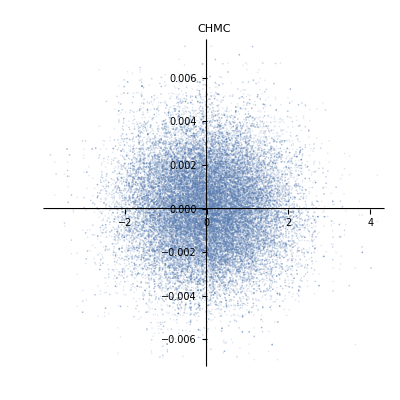

{0.995341,0.989029,1.04221,0.946285,0.686583,0.775366,0.905602,0.943391,0.9864,0.992241}

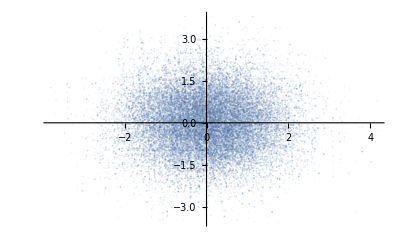

```mathematica
QS=hmc[U,dU,ddU,10,5000,10000,True,True];
Table[1/4^(i-1),{i,1,10}]//N
Diagonal[Covariance[QS]]
ListPlot[QS[[;;,{1,10}]],PlotLabel->CHMC,PlotStyle->Opacity[.2],AspectRatio->1]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1[[;;,{1,10}]],PlotStyle->Opacity[.1]]
```

501 422251. 60.9427 0.200437 0.421409 4691.68 426943. 1.23654×10^6 0.0000137806 0.0001 True {1,3,4,7,11} {1,11}

1002 181999. 65.3355 0.509743 0.359141 1838.54 183838. 1.23654×10^6 4.39093×10^-6 0.0001 True {1,4,5,6,11} {1,11}

1503 109672. 42.1984 0.513368 0.45127 1109.48 110781. 1.23654×10^6 5.84432×10^-6 0.0001 True {1,10,11} {1,11}

2004 80921. 39.6957 0.68049 0.304038 818.426 81739.4 1.23654×10^6 5.31302×10^-6 0.0001 True {1,3,5,10,11} {1,11}

2505 64198.7 44.8901 0.386319 0.375867 646.361 64845. 1.23654×10^6 7.07163×10^-6 0.0001 True {1,3,5,11} {1,11}

3006 55727.1 50.2328 0.672837 0.319641 563.59 56290.7 1.23654×10^6 5.84432×10^-6 0.0001 True {1,7,8,11} {1,11}

3507 48470.2 54.7795 0.827216 0.319424 492.473 48962.7 1.23654×10^6 6.42876×10^-6 0.0001 True {2,4,8,9,10,11} {1,11}

4008 42981.2 45.0411 0.520528 0.346223 437.302 43418.5 1.23654×10^6 7.07163×10^-6 0.0001 True {1,2,4,11} {1,11}

4509 37435. 53.173 0.864893 0.206084 380.707 37815.7 1.23654×10^6 7.07163×10^-6 0.0001 True {1,3,4,5,8,11} {1,11}

5010 33916.6 38.9993 0.617936 0.308626 346.733 34263.4 1.23654×10^6 8.55668×10^-6 0.0001 True {1,3,4,5,7,11} {1,11}

5511 33940.2 36.326 0.578267 0.337747 323.155 34263.4 1.23654×10^6 8.55668×10^-6 0.0001 True {1,2,5,6,11} {1,11}

6012 33970.6 36.4899 0.753153 0.262009 292.809 34263.4 1.23654×10^6 8.55668×10^-6 0.0001 True {1,5,7,11} {1,11}

6513 33980.7 52.5576 0.629494 0.349003 282.644 34263.4 1.23654×10^6 8.55668×10^-6 0.0001 True {1,2,6,9,11} {1,11}

7014 33982.2 55.3105 0.447566 0.352719 281.139 34263.4 1.23654×10^6 8.55668×10^-6 0.0001 True {1,2,4,11} {1,11}

7515 34005.7 41.8325 0.69416 0.297015 257.705 34263.4 1.23654×10^6 8.55668×10^-6 0.0001 True {1,3,4,8,11} {1,11}

8016 34015.7 44.3257 0.606025 0.266105 247.715 34263.4 1.23654×10^6 8.55668×10^-6 0.0001 True {1,2,5,11} {1,11}

8517 34027.8 54.1824 0.7997 0.321863 235.551 34263.4 1.23654×10^6 8.55668×10^-6 0.0001 True {1,5,6,8,11} {1,11}

9018 34032.5 48.7479 0.502205 0.301255 230.874 34263.4 1.23654×10^6 8.55668×10^-6 0.0001 True {1,3,8,9} {1,11}

9519 34048. 58.3256 0.685137 0.320075 215.401 34263.4 1.23654×10^6 8.55668×10^-6 0.0001 True {1,2,5,9,11} {1,11}

{1.,0.25,0.0625,0.015625,0.00390625,0.000976563,0.000244141,0.0000610352,0.0000152588,3.8147×10^-6}

{0.795552,0.42854,1.33864,0.240901,0.0161354,0.000890122,0.000197162,0.0000635359,0.0000150643,3.79872×10^-6}

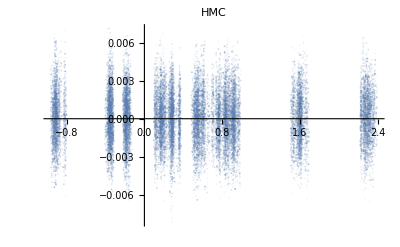

{0.891937,1.30926,4.62798,3.92653,2.0324,0.954717,0.898652,1.02028,0.993607,0.997904}

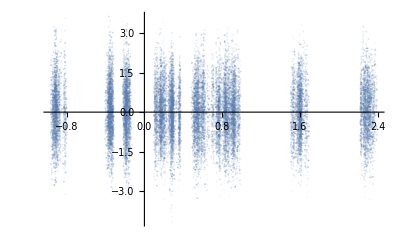

```mathematica
QS=hmc[U,dU,ddU,10,5000,10000,True,False];
Table[1/4^(i-1),{i,1,10}]//N
Diagonal[Covariance[QS]]
ListPlot[QS[[;;,{1,10}]],PlotLabel->HMC,PlotStyle->Opacity[.1]]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1[[;;,{1,10}]],PlotStyle->Opacity[.1]]
```

501 2.85983×10^6 3.95752 0.2 0.421637 932263. 2.55503×10^6 3.79209×10^6 1.×10^-9 0.00881975 False {1,2,3,7,9} {1,10,11}

1002 1.34183×10^6 4.42392 0.3 0.483046 283662. 2.55503×10^6 1.6255×10^6 1.×10^-9 0.00728905 False {1,2,5,11} {1,11}

1503 453776. 3.3266 0.100001 0.316227 145262. 2.55503×10^6 599039. 1.×10^-9 0.00452593 False {1,2,4,8} {1,11}

2004 304591. 9.05296 0.2 0.421637 86037.2 2.55503×10^6 390628. 1.×10^-9 0.00602401 False {1,2,5,11} {1,11}

2505 157141. 3.48539 0.2 0.421637 41083.4 2.55503×10^6 198224. 1.×10^-9 0.00662641 False {1,2,3,8,10} {1,11}

3006 87972.7 9.13239 0.231977 0.41687 20184.4 2.55503×10^6 108157. 1.×10^-9 0.00662641 False {1,2,6,8,11} {1,3,11}

3507 31617.4 2.6086 0.00729038 0.009598 8779.49 2.55503×10^6 40396.9 1.×10^-9 0.00602401 False {1,2,3,4} {11}

4008 17752.4 6.68536 0.387415 0.446525 4275.29 2.55503×10^6 22027.7 1.×10^-9 0.00602401 False {1,2,3,4,8,11} {1,2,10,11}

4509 12827.3 5.39528 0.417595 0.402919 1924.1 2.55503×10^6 14751.4 1.×10^-9 0.00547637 False {1,2,5,10,11} {1,11}

5010 13392.9 4.87715 0.482936 0.403727 1358.47 2.55503×10^6 14751.4 1.×10^-9 0.00255477 False {1,9,10,11} {1,11}

5511 13672.6 9.51219 0.612849 0.292696 1078.78 2.55503×10^6 14751.4 1.×10^-9 0.00255477 False {1,2,5,11} {1,11}

6012 13887.3 6.518 0.588928 0.443206 864.108 2.55503×10^6 14751.4 1.×10^-9 0.00232252 False {1,8,11} {1,11}

6513 14033.2 6.99869 0.514665 0.41443 718.195 2.55503×10^6 14751.4 1.×10^-9 0.00255477 False {1,2,3,6,7,11} {1,11}

7014 15571.9 6.00034 0.546265 0.401704 582.664 2.55503×10^6 16154.6 1.×10^-9 0.00255477 False {1,2,4,5,7,11} {1,11}

7515 15670.6 4.93085 0.530309 0.356525 483.965 2.55503×10^6 16154.6 1.×10^-9 0.00340039 False {1,3,4,7,10,11} {1,11}

8016 15737.2 8.39921 0.859785 0.318928 417.346 2.55503×10^6 16154.6 1.×10^-9 0.00211138 False {1,4,7,8,11} {1,11}

8517 15818.3 5.81986 0.70398 0.340135 336.292 2.55503×10^6 16154.6 1.×10^-9 0.00232252 False {1,3,4,6,7} {1,11}

9018 15864.1 6.0899 0.629842 0.443519 290.44 2.55503×10^6 16154.6 1.×10^-9 0.00281024 False {1,8,10,11} {1,11}

9519 15897.7 10.4874 0.666206 0.386616 256.844 2.55503×10^6 16154.6 1.×10^-9 0.00211138 False {1,2,6,11} {1,11}

10020 17511.7 9.52159 0.541712 0.362954 232.71 2.55503×10^6 17744.4 1.×10^-9 0.00255477 False {1,3,4,9,11} {1,11}

10521 17560.2 3.85456 0.619577 0.340913 184.14 2.55503×10^6 17744.4 1.×10^-9 0.00255477 False {1,3,5,7,9,11} {1,11}

11022 16430.5 7.86285 0.713326 0.360313 166.744 2.55503×10^6 16597.3 1.×10^-9 0.00211138 False {1,3,6,9,11} {1,11}

11523 13925. 7.93852 0.525009 0.367172 143.025 2.55503×10^6 14068. 1.×10^-9 0.00255477 False {1,2,8,11} {1,11}

12024 11865.4 10.5796 0.642369 0.348127 128.584 2.55503×10^6 11994. 1.×10^-9 0.00255477 False {1,2,7,10,11} {1,11}

12525 9697.93 6.51211 0.769141 0.30726 103.255 2.55503×10^6 9801.18 1.×10^-9 0.00281024 False {1,4,5,7,11} {1,11}

13026 7640.07 12.5311 0.516034 0.448315 89.5732 2.55503×10^6 7729.65 1.×10^-9 0.00374043 False {1,2,6,9,11} {1,11}

13527 6054.74 6.49864 0.461648 0.419031 68.1829 2.55503×10^6 6122.93 1.×10^-9 0.00411448 False {1,2,5,6,11} {1,11}

14028 4354.1 7.87209 0.485383 0.362487 48.605 2.55503×10^6 4402.71 1.×10^-9 0.00452593 False {1,2,6,8} {1,11}

14529 3621.29 7.27626 0.661735 0.359781 40.35 2.55503×10^6 3661.64 1.×10^-9 0.00374043 False {1,4,8,10,11} {1,11}

15030 2771.24 6.60943 0.433108 0.360191 37.0275 2.55503×10^6 2808.26 1.×10^-9 0.00497852 False {1,6,9} {1,11}

15531 2778.64 6.33099 0.597443 0.409387 29.6222 2.55503×10^6 2808.26 1.×10^-9 0.00497852 False {1,3,11} {1,11}

16032 2776.38 8.32578 0.584512 0.431095 31.8795 2.55503×10^6 2808.26 1.×10^-9 0.00497852 False {1,2,6,9,11} {1,11}

16533 2782.94 7.65159 0.620096 0.404226 25.3225 2.55503×10^6 2808.26 1.×10^-9 0.00497852 False {1,2,4,9,11} {1,11}

17034 2782. 6.11212 0.517928 0.406394 26.2663 2.55503×10^6 2808.26 1.×10^-9 0.00497852 False {1,2,3,11} {1,11}

17535 2780.74 10.1489 0.574852 0.42902 27.5271 2.55503×10^6 2808.26 1.×10^-9 0.00497852 False {1,2,8,10,11} {1,11}

18036 2781.54 3.72034 0.607288 0.367707 26.7257 2.55503×10^6 2808.26 1.×10^-9 0.00497852 False {1,5,6,9,11} {1,11}

18537 2777.21 10.5827 0.661152 0.408455 31.0488 2.55503×10^6 2808.26 1.×10^-9 0.00497852 False {1,11} {1,11}

19038 2790.53 7.01011 0.811142 0.303247 17.7338 2.55503×10^6 2808.26 1.×10^-9 0.00497852 False {1,3,4,6,7,10,11} {1,11}

19539 2780.92 6.16369 0.706691 0.366151 27.3433 2.55503×10^6 2808.26 1.×10^-9 0.00497852 False {1,8,11} {1,11}

{1.,0.25,0.0625,0.015625,0.00390625,0.000976563,0.000244141,0.0000610352,0.0000152588,3.8147×10^-6}

{1.00031,0.241759,0.0566403,0.014332,0.00242472,0.000215808,0.0000269744,2.08715×10^-6,5.61831×10^-7,4.20328×10^-7}

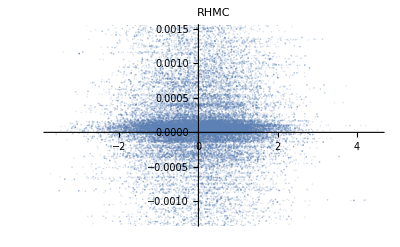

{1.00015,0.98338,0.951969,0.957732,0.787863,0.470093,0.332396,0.184921,0.191886,0.331943}

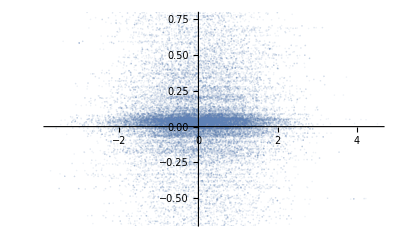

```mathematica
QS=hmc[U,dU,ddU,10,15000,20000,False,False];
Table[1/4^(i-1),{i,1,10}]//N
Diagonal[Covariance[QS]]
ListPlot[QS[[;;,{1,10}]],PlotLabel->RHMC,PlotStyle->Opacity[.2]]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1[[;;,{1,10}]],PlotStyle->Opacity[.1]]
```